```mathematica
(*(ccdata[7]/.{x_,y_}/;x>maxyx->{x,0})[[All,2]]*)
```

```mathematica
SetDirectory[ParentDirectory[NotebookDirectory[]]];
```

## Define Functions

```mathematica
BW[w_,wr_,Γ_,δbg_,const_,shift_,shift2_]:=
const((Γ/2)^2/((w-wr)^2+(Γ/2)^2))+ δbg((Γ/2)(w-wr))/((w-wr)^2+(Γ/2)^2)+0 ((4 (w-wr)^2- Γ^2) deltabg^2)/(4 (w-wr)^2+Γ^2)+shift (w-wr)+shift2 ;
BWi[w_,wr_,Γ_,const_]:=const((Γ/2)^2/((w-wr)^2+(Γ/2)^2)) ;

fitnew[input_,output_,Tscan_]:=Module[{temp=Range[1,Length[Tscan]],n,maxx,minx,maxy,maxyx,maxyi,maxxy,inter,maxxs,maxxis,maxys,mins,hwhmi,gammas,inputc,bad},
SetSharedVariable[temp];
ParallelDo[n=temp[[ii]];
maxx=Max[input[n][[All,1]]];
minx=Min[input[n][[All,1]]];
maxy=Max[input[n][[All,2]]];
maxyx=input[n][[Position[input[n],Max[input[n][[All,2]]]][[1,1]],1]];
maxyi=Position[input[n][[All,1]],maxyx][[1,1]];
maxxy=input[n][[Position[input[n],Max[input[n][[All,1]]]][[1,1]],2]];
inter=Interpolation[input[n],InterpolationOrder->1];maxxs=Sort[Quiet[DeleteDuplicatesBy[Table[{Round[FindMaxValue[{inter[x],maxyx≤x≤maxx},{x,a}],maxxy],FindArgMax[{inter[x],maxyx≤x≤maxx},{x,a}][[1]]},{a,maxyx,maxx,(maxx-maxyx)/50}],First][[All,2]]]];
bad={};
If[Length[maxxs]>1,Do[If[maxxs[[i+1]]/maxxs[[i]]≤1.001,bad=Append[bad,{i}]],{i,Length[maxxs]-1}]];
maxxs=Delete[maxxs,bad];maxxis=Sort[Table[Position[input[n][[All,1]],Nearest[input[n][[All,1]],maxxs[[i]]][[1]]][[1,1]],{i,Length[maxxs]}]];
bad={};
Do[If[Or[input[n][[maxxis[[i]]-30,2]]>input[n][[maxxis[[i]],2]],input[n][[maxxis[[i]]+30,2]]>input[n][[maxxis[[i]],2]]],bad=Append[bad,{i}]],{i,Length[maxxis]}];maxxs=Delete[maxxs,bad];maxxis=Delete[maxxis,bad];
maxys=Table[input[n][[maxxis[[i]],2]],{i,Length[maxxs]}];
If[Length[maxxs]>1,
mins=Range[Length[maxxs]-1];
Do[mins[[i]]=Position[input[n][[All,2]],Min[input[n][[maxxis[[i]];;maxxis[[i+1]],2]]]][[1,1]],{i,Length[maxxs]-1}];mins=Append[Prepend[mins,maxxis[[1]]-(mins[[1]]-maxxis[[1]])],If[maxxis[[-1]]+(maxxis[[-1]]-mins[[-1]])≤ Length[input[n]],maxxis[[-1]]+(maxxis[[-1]]-mins[[-1]]),Length[input[n]]]];,
hwhmi=Position[input[n],Nearest[input[n][[;;maxyi,2]],maxy/2][[1]]][[1,1]];
mins={maxyi-3(maxyi-hwhmi),If[maxyi+3(maxyi-hwhmi)≤Length[input[n]],maxyi+3(maxyi-hwhmi),Length[input[n]]]};];
If[mins[[1]]<0,mins[[1]]=1];
hwhmi=Range[Length[maxxs]];
Do[hwhmi[[i]]=Position[input[n],Nearest[input[n][[mins[[i]];;maxxis[[i]],2]],inter[maxxs[[i]]]/2][[1]]][[1,1]],{i,Length[maxxs]}];
gammas=Range[Length[hwhmi]];
Do[gammas[[i]]=2(maxxs[[i]]-input[n][[hwhmi[[i]],1]]),{i,Length[hwhmi]}];
inputc=Range[Length[maxxs]];
Do[inputc[[i]]=input[n][[If[i≥2,If[maxxis[[i]]-3(maxxis[[i]]-hwhmi[[i]])<mins[[i]],mins[[i]],maxxis[[i]]-3(maxxis[[i]]-hwhmi[[i]])],If[maxxis[[i]]-3(maxxis[[i]]-hwhmi[[i]])>0,maxxis[[i]]-3(maxxis[[i]]-hwhmi[[i]]),1]];;If[maxxis[[i]]+3(maxxis[[i]]-hwhmi[[i]])<mins[[i+1]],maxxis[[i]]+3(maxxis[[i]]-hwhmi[[i]]),mins[[i+1]]]]],{i,Length[maxxs]}];
temp[[ii]]=Range[Length[hwhmi]];
Do[temp[[ii,i]]=NonlinearModelFit[inputc[[i]],{BW[w,wr,Γ,δbg,const,shift,shift2],const>0,Γ>0},{{wr,maxxs[[i]]},{Γ,gammas[[i]]},{const,maxys[[i]]},{δbg,0.0},{shift,0.0},{shift2,0.0}},w,MaxIterations->1000],{i,Length[hwhmi]}];Print[ii];,{ii,Length[Tscan]}];output=temp;];

store[param_,res_,model_]:=Module[{temp=ToString[res]},res=Range[Length[model]];
Do[res[[i]]=Range[Length[model[[i]]]],{i,Length[model]}];Do[Do[res[[i,ii]]=param/.model[[i,ii]]["BestFitParameters"],{ii,Length[res[[i]]]}],{i,Length[res]}];Export["spectraldata/Tscan/results/"<>temp<>".dat",res];];

storearea[res_,model_]:=Module[{temp=ToString[res]},res=Range[Length[model]];
Do[res[[i]]=Range[Length[model[[i]]]],{i,Length[model]}];Do[Do[res[[i,ii]]=π/2(Γ/.model[[i,ii]]["BestFitParameters"])( const/.model[[i,ii]]["BestFitParameters"]),{ii,Length[res[[i]]]}],{i,Length[res]}];Export["spectraldata/Tscan/results/"<>temp<>".dat",res];];

import[res_]:=res=Import["spectraldata/Tscan/results/"<>ToString[res]<>".dat"];
```

## Charmonium

### Import Data

```mathematica
Tscanc=Round[1000 Join[Table[i,{i,0.15,0.16,0.001}],{0.162},Table[i,{i,0.164,0.170,0.003}],Table[i,{i,0.1740,0.2220,0.003}],Table[i,{i,0.224,0.230,0.003}],Table[i,{i,0.234,0.249,0.003}],Table[i,{i,0.253,0.3,0.003}]]]
```

{150,151,152,153,154,155,156,157,158,159,160,162,164,167,170,174,177,180,183,186,189,192,195,198,201,204,207,210,213,216,219,222,224,227,230,234,237,240,243,246,249,253,256,259,262,265,268,271,274,277,280,283,286,289,292,295,298}

```mathematica
Do[ccdata[n]=Import["spectraldata/Tscan/cc/swccT"<>ToString[Tscanc[[n]]]<>"spectra.dat"];,{n,Length[Tscanc]}];
Manipulate[ListPlot[ccdata[n],Joined->True],{n,1,Length[Tscanc],1}]
```

```mathematica
Do[ccdatau[n]=Import["spectraldata/Tscan/cc/swccT"<>ToString[Tscanc[[n]]]<>"uspectra.dat"];,{n,Length[Tscanc]}];
Manipulate[ListPlot[ccdatau[n],Joined->True],{n,1,Length[Tscanc],1}]
```

```mathematica
Do[ccdatal[n]=Import["spectraldata/Tscan/cc/swccT"<>ToString[Tscanc[[n]]]<>"lspectra.dat"];,{n,Length[Tscanc]}];
Manipulate[ListPlot[ccdatal[n],Joined->True],{n,1,Length[Tscanc],1}]
```

### Fitting

```mathematica
Clear[ccmodelu,ccmodell,ccmodel]
fitnew[ccdata,ccmodel,Tscanc];
fitnew[ccdatal,ccmodell,Tscanc];
fitnew[ccdatau,ccmodelu,Tscanc];
```

### Store Results

```mathematica
Do[If[Length[ccmodel[[i]]]>2,ccmodel[[i]]=ccmodel[[i,;;2]]];If[Length[ccmodelu[[i]]]>2,ccmodelu[[i]]=ccmodelu[[i,;;2]]];If[Length[ccmodell[[i]]]>2,ccmodell[[i]]=ccmodell[[i,;;2]]];,{i,Length[ccmodel]}];
```

```mathematica
Clear[wrfitcc,wrfitccl,wrfitccu,gfitcc,gfitccl,gfitccu,areafitcc,areafitccu,areafitccl,cfitcc,cfitccl,cfitccu,dfitcc,dfitccl,dfitccu,sfitcc,sfitccl,sfitccu,s2fitcc,s2fitccl,s2fitccu];
store[wr,wrfitcc,ccmodel];
store[wr,wrfitccl,ccmodell];
store[wr,wrfitccu,ccmodelu];
store[Γ,gfitcc,ccmodel];
store[Γ,gfitccl,ccmodell];
store[Γ,gfitccu,ccmodelu];
store[const,cfitcc,ccmodel];
store[const,cfitccl,ccmodell];
store[const,cfitccu,ccmodelu];
store[δbg,dfitcc,ccmodel];
store[δbg,dfitccl,ccmodell];
store[δbg,dfitccu,ccmodelu];
store[shift,sfitcc,ccmodel];
store[shift,sfitccl,ccmodell];
store[shift,sfitccu,ccmodelu];
store[shift2,s2fitcc,ccmodel];
store[shift2,s2fitccl,ccmodell];
store[shift2,s2fitccu,ccmodelu];
storearea[areafitcc,ccmodel];
storearea[areafitccl,ccmodell];
storearea[areafitccu,ccmodelu];
```

### Display Results

```mathematica
(*import[wrfitcc];
import[wrfitccl];
import[wrfitccu];
import[gfitcc];
import[gfitccl];
import[gfitccu];
import[cfitcc];
import[cfitccl];
import[cfitccu];
import[dfitcc];
import[dfitccl];
import[dfitccu];
import[sfitcc];
import[sfitccl];
import[sfitccu];
import[s2fitcc];
import[s2fitccl];
import[s2fitccu];
import[areafitcc];
import[areafitccl];
import[areafitccu];*)
```

```mathematica
Do[If[Length[wrfitcc[[-i]]]<2,cc1Tcut=Length[wrfitcc]-i];,{i,Length[wrfitcc]}];
Do[If[Length[wrfitccu[[-i]]]<2,cc1uTcut=Length[wrfitccu]-i];,{i,Length[wrfitccl]}];
Do[If[Length[wrfitccl[[-i]]]<2,cc1lTcut=Length[wrfitccl]-i];,{i,Length[wrfitccu]}];
```

```mathematica
Manipulate[Show[{ListPlot[ccdata[i],Joined->True],Plot[BW[x,wrfitcc[[i,ii]],gfitcc[[i,ii]],dfitcc[[i,ii]],cfitcc[[i,ii]],sfitcc[[i,ii]],s2fitcc[[i,ii]]],{x,0.7wrfitcc[[i,ii]],1.3wrfitcc[[i,ii]]},PlotStyle->{Red,Dashed},PlotRange->All],Plot[BWi[x,wrfitcc[[i,ii]],gfitcc[[i,ii]],cfitcc[[i,ii]]],{x,0.7wrfitcc[[i,ii]],1.3wrfitcc[[i,ii]]},PlotStyle->{Green,Dashed},PlotRange->All]}],{i,1,Length[wrfitcc],1},{ii,1,Length[wrfitcc[[1]]],1}]
```

```mathematica
Manipulate[Show[{ListPlot[ccdatau[i],Joined->True],Plot[BW[x,wrfitccu[[i,ii]],gfitccu[[i,ii]],dfitccu[[i,ii]],cfitccu[[i,ii]],sfitccu[[i,ii]],s2fitccu[[i,ii]]],{x,0.7wrfitccu[[i,ii]],1.3wrfitccu[[i,ii]]},PlotStyle->{Red,Dashed},PlotRange->All],Plot[BWi[x,wrfitccu[[i,ii]],gfitccu[[i,ii]],cfitccu[[i,ii]]],{x,0.7wrfitccu[[i,ii]],1.3wrfitccu[[i,ii]]},PlotStyle->{Green,Dashed},PlotRange->All]}],{i,1,Length[wrfitccu],1},{ii,1,Length[wrfitccu[[1]]],1}]
```

```mathematica
cccont={3.648553230970728,3.628792315589096,3.6102772374036665,3.592872558615657,3.576462604611754,3.5609479062546994,3.5462423968160763,3.5322711829829765,3.5189687484274836,3.50627749401972,3.4941465499919833,3.471390082559803,3.4404770981602106,3.412745256022291,3.3876075252547677,3.364618948412143,3.3434352822109226,3.323785454856247,3.3054526994473723,3.288261308642187,3.272067135253791,3.2567506466093215,3.2422117602027,3.2283659447979494,3.2151412362308114,3.2027178984093014,3.191176351511658,3.1800210358114978,3.1692213413581785,3.158750046801837,3.1485828474763107,3.138697962475392,3.1290758041221385,3.1196986990116966,3.1105506514104317,3.1016171414292035,3.0928849538048953,3.0843420286931376,3.0759773300200837,3.067780741067037,3.0597429617989613,3.051855425801331,3.0441102296733202,3.0365000618906883,3.0290181515134766,3.0216582135930583,3.0144144050429746,3.00728128686385,3.00025378432098,2.9933271604368104,2.9864969822394043,2.979759099825311,2.973109619884775,2.966544887282899,2.9600614652455026,2.9536561196905122,2.947325800789547};
```

```mathematica
cccontl={4.048708930682597,4.009316803905209,3.9735736213919575,3.940935189429301,3.910964192547662,3.883304683840814,3.857663640121338,3.8337973843831685,3.811501414240311,3.7906026708167775,3.7709535982888998,3.734915017284229,3.6875661410999436,3.6465446267420014,3.610458248407371,3.5783090693016173,3.549360830493372,3.5230570042405347,3.498968136718897,3.4767568706999414,3.456154044353856,3.4369419476959586,3.418942337736571,3.4020076937737724,3.386014727052341,3.371196391013642,3.3576445499895993,3.3446574515287284,3.3321857750631403,3.3201861428470045,3.308620225299813,3.297454006909004,3.286657177806799,3.2762026271363154,3.2660660187345543,3.256225433543098,3.246661069010202,3.2373549806996387,3.2282908576590206,3.219453842580342,3.210830360934706,3.2024079818876814,3.1941753003680837,3.1861218221142042,3.1782378783540866,3.17051453859662,3.1629435395466765,3.1555172242922174,3.1482284802349816,3.1410706960946166,3.134037710266731,3.12712377723629,3.1203235273265597,3.113631937890117,3.1070443031761004,3.1005562102325395,3.094163511471234};
```

```mathematica
cccontu={3.4493785176747487,3.4350160355264046,3.4213875934294187,3.4084246818865873,3.3960674738508696,3.3842634557432545,3.3729663154018468,3.362135032919271,3.3517331263885457,3.341728022197106,3.3320905317756675,3.313816003962213,3.2885826103736058,3.2655453893871704,3.2443364834259896,3.224669779224004,3.2063188887287652,3.189101977337091,3.1728710563832934,3.1575042645925784,3.1429002008036258,3.128973691485115,3.115652583032802,3.1028752776287822,3.0905888170280154,3.0789481931578315,3.068025732985631,3.057413621238581,3.047088652261219,3.037030063858444,3.0272192122073713,3.0176392990669836,3.0082751404081245,2.999112969699187,2.990140269896058,2.981345629154585,2.972718617839826,2.964249680471857,2.955930039545467,2.9477516198205818,2.9397069722027163,2.9317892124728613,2.9239919691419036,2.9163093298389375,2.908735803364327,2.9012662782896452,2.893895989672094,2.8866204905405257,2.879435621297975,2.8723374897819616,2.865322445081371,2.8583870616666847,2.8515281187828547,2.8447425862877624,2.8380276092165095,2.8313804956150546,2.824798702052603};
```

```mathematica
ccbind=cccont-wrfitcc;
ccbindu=cccontu-wrfitccu;
ccbindl=cccontl-wrfitccl;
```

```mathematica
Do[If[(ccbind-gfitcc)[[i,1]]>0,cc1Tmelt=i],{i,1,Length[ccbind]}];
Do[If[(ccbind-gfitcc)[[i,2]]>0,cc2Tmelt=i],{i,1,cc1Tcut}];
Do[If[(ccbindl-gfitccl)[[i,1]]>0,cc1lTmelt=i],{i,1,Length[ccbind]}];
Do[If[(ccbindl-gfitccl)[[i,2]]>0,cc2lTmelt=i],{i,1,cc1lTcut}];
Do[If[(ccbindu-gfitccu)[[i,1]]>0,cc1uTmelt=i],{i,1,Length[ccbind]}];
Do[If[(ccbindu-gfitccu)[[i,2]]>0,cc2uTmelt=i,cc2uTmelt=1],{i,1,cc1uTcut}];
```

```mathematica
N[{Tscanc[[cc1lTmelt]],Tscanc[[cc1Tmelt]],Tscanc[[cc1uTmelt]]}/155]
```

{1.82581,1.48387,1.29677}

```mathematica
N[{Tscanc[[cc2lTmelt]],Tscanc[[cc2Tmelt]],Tscanc[[cc2uTmelt]]}/155]
```

{1.07742,0.974194,0.967742}

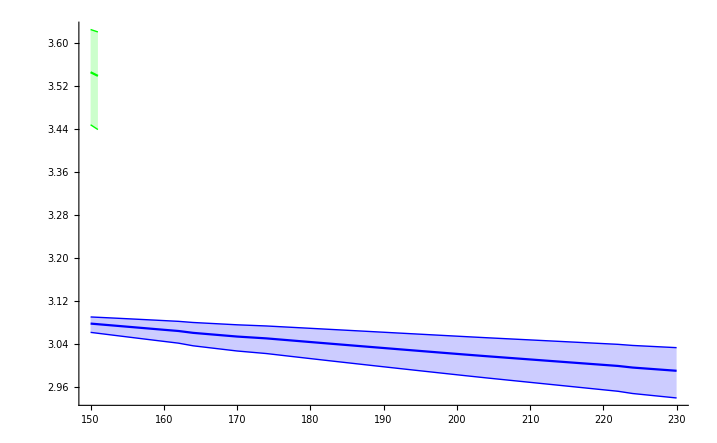

```mathematica
ListPlot[{Transpose[{Tscanc[[;;cc1Tmelt]],wrfitcc[[;;cc1Tmelt,1]]}],Transpose[{Tscanc[[;;cc1Tmelt]],wrfitccl[[;;cc1Tmelt,1]]}],Transpose[{Tscanc[[;;cc1Tmelt]],wrfitccu[[;;cc1Tmelt,1]]}],Transpose[{Tscanc[[;;cc2Tmelt]],wrfitcc[[;;cc2Tmelt,2]]}],Transpose[{Tscanc[[;;cc2Tmelt]],wrfitccl[[;;cc2Tmelt,2]]}],Transpose[{Tscanc[[;;cc2Tmelt]],wrfitccu[[;;cc2Tmelt,2]]}]},PlotRange->All,Filling->{1->{2},1->{3},4->{5},4->{6}},FillingStyle->Opacity[0.2],PlotStyle->{Blue,{Blue,Thin},{Blue,Thin},Green,{Green,Thin},{Green,Thin}},Joined->True]
```

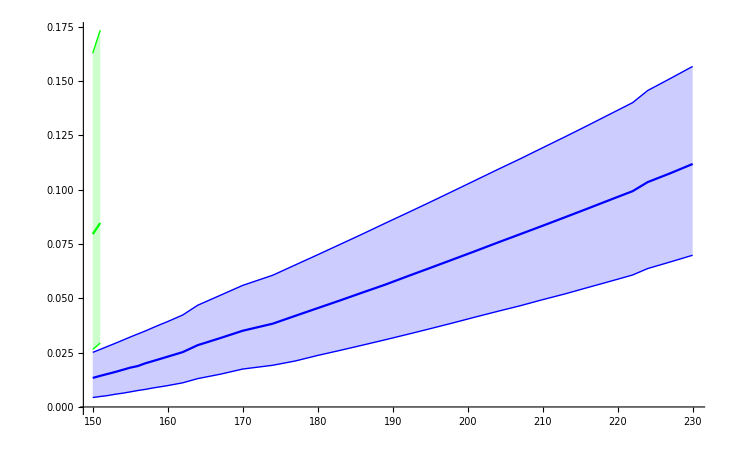

```mathematica
ListPlot[{Transpose[{Tscanc[[;;cc1Tmelt]],gfitcc[[;;cc1Tmelt,1]]}],Transpose[{Tscanc[[;;cc1Tmelt]],gfitccl[[;;cc1Tmelt,1]]}],Transpose[{Tscanc[[;;cc1Tmelt]],gfitccu[[;;cc1Tmelt,1]]}],Transpose[{Tscanc[[;;cc2Tmelt]],gfitcc[[;;cc2Tmelt,2]]}],Transpose[{Tscanc[[;;cc2Tmelt]],gfitccl[[;;cc2Tmelt,2]]}],Transpose[{Tscanc[[;;cc2Tmelt]],gfitccu[[;;cc2Tmelt,2]]}]},PlotRange->All,Filling->{1->{2},1->{3},4->{5},4->{6}},FillingStyle->Opacity[0.2],PlotStyle->{Blue,{Blue,Thin},{Blue,Thin},Green,{Green,Thin},{Green,Thin}},Joined->True]
```

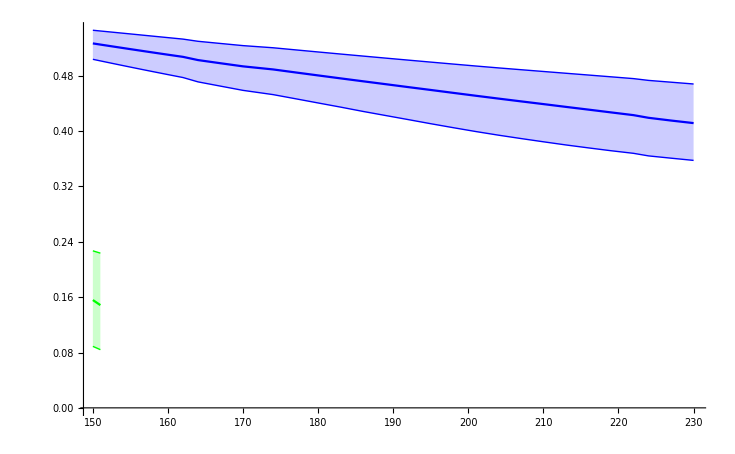

```mathematica
ListPlot[{Transpose[{Tscanc[[;;cc1Tmelt]],areafitcc[[;;cc1Tmelt,1]]}],Transpose[{Tscanc[[;;cc1Tmelt]],areafitccl[[;;cc1Tmelt,1]]}],Transpose[{Tscanc[[;;cc1Tmelt]],areafitccu[[;;cc1Tmelt,1]]}],Transpose[{Tscanc[[;;cc2Tmelt]],areafitcc[[;;cc2Tmelt,2]]}],Transpose[{Tscanc[[;;cc2Tmelt]],areafitccl[[;;cc2Tmelt,2]]}],Transpose[{Tscanc[[;;cc2Tmelt]],areafitccu[[;;cc2Tmelt,2]]}]},PlotRange->All,Filling->{1->{2},1->{3},4->{5},4->{6}},FillingStyle->Opacity[0.2],PlotStyle->{Blue,{Blue,Thin},{Blue,Thin},Green,{Green,Thin},{Green,Thin}},Joined->True]
```

### Emission Rates

```mathematica
Emfactor=2.356447552594432;
nB[w_,T_]:=1/(Exp[w/T]-1);
```

```mathematica
R0=ConstantArray[0,cc1Tcut];
Do[R0[[ii]]={Tscanc[[ii]],Emfactor (areafitcc[[ii,2]]nB[wrfitcc[[ii,2]],Tscanc[[ii]]/1000])/(areafitcc[[ii,1]]nB[wrfitcc[[ii,1]],Tscanc[[ii]]/1000])},{ii,cc1Tcut}];
```

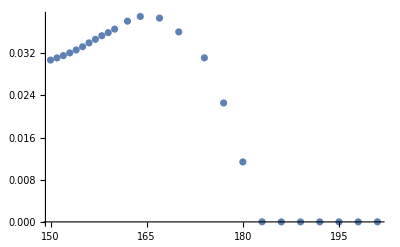

```mathematica
ListPlot[R0]
```

## Bottomonium

```mathematica
Tscanb=IntegerPart[1000 Table[i,{i,0.15,0.6,0.005}]]
```

{150,155,160,164,169,175,180,185,190,195,200,205,210,215,220,224,229,235,240,245,250,255,260,265,270,275,280,285,290,295,300,305,310,315,320,325,329,334,339,345,350,355,360,365,370,375,380,385,390,395,400,405,410,415,420,425,430,435,439,444,449,454,459,464,470,475,480,485,490,495,500,505,510,515,520,525,530,535,540,545,550,555,560,565,570,575,580,585,590,595,600}

```mathematica
Do[bbdata[n]=Import["spectraldata/Tscan/bb/swbbT"<>ToString[Tscanb[[n]]]<>"spectra.dat"];,{n,Length[Tscanb]}];
Manipulate[ListPlot[bbdata[n],Joined->True],{n,1,Length[Tscanb],1}]
```

```mathematica
Do[bbdatal[n]=Import["spectraldata/Tscan/bb/swbbT"<>ToString[Tscanb[[n]]]<>"lspectra.dat"];,{n,Length[Tscanb]}];
Manipulate[ListPlot[bbdatal[n],Joined->True],{n,1,Length[Tscanb],1}]
```

```mathematica
Do[bbdatau[n]=Import["spectraldata/Tscan/bb/swbbT"<>ToString[Tscanb[[n]]]<>"uspectra.dat"];,{n,Length[Tscanb]}];
Manipulate[ListPlot[bbdatau[n],Joined->True],{n,1,Length[Tscanb],1}]
```

### Fitting

```mathematica
Clear[bbmodel,bbmodelu,bbmodell]
fitnew[bbdata,bbmodel,Tscanb];
fitnew[bbdatau,bbmodelu,Tscanb];
fitnew[bbdatal,bbmodell,Tscanb];
```

31

25

1

7

43

19

37

13

26

38

44

32

8

2

14

20

33

27

39

45

21

9

3

28

15

34

40

46

22

16

29

10

4

35

41

47

42

23

36

17

48

5

30

11

18

67

49

61

24

55

6

12

50

68

72

56

82

62

77

87

73

51

69

57

83

63

52

70

78

88

74

71

75

76

58

64

84

53

79

89

59

54

65

90

85

91

80

60

66

86

81

25

19

1

13

7

43

37

31

26

44

38

32

8

2

14

20

27

45

21

39

3

9

33

15

28

22

10

46

40

4

34

29

16

47

41

11

23

35

48

5

12

30

17

42

24

36

49

61

6

55

62

18

63

67

64

65

72

50

66

77

78

56

82

87

83

84

57

88

68

89

73

58

90

51

74

91

79

85

52

69

59

75

76

80

60

53

70

86

71

81

54

43

37

13

19

25

31

1

7

44

38

32

20

14

8

26

2

45

33

39

21

15

9

27

46

3

34

40

22

16

47

35

28

10

4

41

17

23

48

29

36

11

5

24

42

18

30

61

49

12

72

55

77

6

67

62

50

87

82

68

56

73

78

51

63

83

69

57

64

88

74

65

79

52

58

84

70

89

80

75

66

85

59

53

71

90

54

91

76

81

86

60

### Store Results

```mathematica
Do[If[Length[bbmodel[[i]]]>4,bbmodel[[i]]=bbmodel[[i,;;4]]];If[Length[bbmodelu[[i]]]>4,bbmodelu[[i]]=bbmodelu[[i,;;4]]];If[Length[bbmodell[[i]]]>4,bbmodell[[i]]=bbmodell[[i,;;4]]];,{i,Length[bbmodel]}];
```

```mathematica
Clear[wrfitbb,wrfitbbl,wrfitbbu,gfitbb,gfitbbl,gfitbbu,areafitbb,areafitbbu,areafitbbl,cfitbb,cfitbbl,cfitbbu,dfitbb,dfitbbl,dfitbbu,sfitbb,sfitbbl,sfitbbu,s2fitbb,s2fitbbl,s2fitbbu];
store[wr,wrfitbb,bbmodel];
store[wr,wrfitbbl,bbmodell];
store[wr,wrfitbbu,bbmodelu];
store[Γ,gfitbb,bbmodel];
store[Γ,gfitbbl,bbmodell];
store[Γ,gfitbbu,bbmodelu];
store[const,cfitbb,bbmodel];
store[const,cfitbbl,bbmodell];
store[const,cfitbbu,bbmodelu];
store[δbg,dfitbb,bbmodel];
store[δbg,dfitbbl,bbmodell];
store[δbg,dfitbbu,bbmodelu];
store[shift,sfitbb,bbmodel];
store[shift,sfitbbl,bbmodell];
store[shift,sfitbbu,bbmodelu];
store[shift2,s2fitbb,bbmodel];
store[shift2,s2fitbbl,bbmodell];
store[shift2,s2fitbbu,bbmodelu];
storearea[areafitbb,bbmodel];
storearea[areafitbbl,bbmodell];
storearea[areafitbbu,bbmodelu];
```

### Display Results

```mathematica
(*import[wrfitbb];
import[wrfitbbl];
import[wrfitbbu];
import[gfitbb];
import[gfitbbl];
import[gfitbbu];
import[cfitbb];
import[cfitbbl];
import[cfitbbu];
import[dfitbb];
import[dfitbbl];
import[dfitbbu];
import[sfitbb];
import[sfitbbl];
import[sfitbbu];
import[s2fitbb];
import[s2fitbbl];
import[s2fitbbu];
import[areafitbb];
import[areafitbbl];
import[areafitbbu];*)
```

```mathematica
Do[If[Length[wrfitbb[[-i]]]<2,bb1Tcut=Length[wrfitbb]-i];,{i,Length[wrfitbb]}];
Do[If[Length[wrfitbbu[[-i]]]<2,bb1uTcut=Length[wrfitbbu]-i];,{i,Length[wrfitbbu]}];
Do[If[Length[wrfitbbl[[-i]]]<2,bb1lTcut=Length[wrfitbbl]-i];,{i,Length[wrfitbbl]}];
Do[If[Length[wrfitbb[[-i]]]<3,bb2Tcut=Length[wrfitbb]-i];,{i,Length[wrfitbb]}];
Do[If[Length[wrfitbbu[[-i]]]<3,bb2uTcut=Length[wrfitbbu]-i];,{i,Length[wrfitbbu]}];
Do[If[Length[wrfitbbl[[-i]]]<3,bb2lTcut=Length[wrfitbbl]-i];,{i,Length[wrfitbbl]}];
Do[If[Length[wrfitbb[[-i]]]<4,bb3Tcut=Length[wrfitbb]-i];,{i,Length[wrfitbb]}];Do[If[Length[wrfitbbu[[-i]]]<4,bb3uTcut=Length[wrfitbbu]-i];,{i,Length[wrfitbbu]}];Do[If[Length[wrfitbbl[[-i]]]<4,bb3lTcut=Length[wrfitbbl]-i];,{i,Length[wrfitbbl]}];
```

```mathematica
Manipulate[Show[{ListPlot[bbdata[i],Joined->True],Plot[BW[x,wrfitbb[[i,ii]],gfitbb[[i,ii]],dfitbb[[i,ii]],cfitbb[[i,ii]],sfitbb[[i,ii]],s2fitbb[[i,ii]]],{x,0.7wrfitbb[[i,ii]],1.3wrfitbb[[i,ii]]},PlotStyle->{Red,Dashed},PlotRange->All],Plot[BWi[x,wrfitbb[[i,ii]],gfitbb[[i,ii]],cfitbb[[i,ii]]],{x,0.7wrfitbb[[i,ii]],1.3wrfitbb[[i,ii]]},PlotStyle->{Green,Dashed},PlotRange->All]}],{i,1,Length[wrfitbb],1},{ii,1,Length[wrfitbb[[1]]],1}]
```

```mathematica
bbcont={10.47459661653534,10.386991291819312,10.320189935556595,10.266520483724824,10.221771783701307,10.183415247448838,10.14982884042086,10.119917801704643,10.092912804537864,10.068255145767312,10.045527844650223,10.024869142170065,10.00606442137611,9.988248930352256,9.971300912748175,9.955119189686751,9.939618860084348,9.924728047184722,9.91038541425775,9.896538234463003,9.883140878360269,9.870153615237932,9.857541654132588,9.84527436973816,9.833324672428462,9.821668491664653,9.810284349405235,9.799153005449387,9.788257160460661,9.777581207953114,9.76711102016143,9.756833770672042,9.746737782242517,9.736812392434949,9.727047840979282,9.717435173901784,9.7079661552598,9.698633193697498,9.68942927922979,9.680347923072885,9.67138310961781,9.662529251650565,9.653781149410847,9.645133958371117,9.636583155264336,9.628124512339577,9.61975407153492,9.611468121959486,9.603263180915544,9.595135974071855,9.587083421208572,9.579102619219741,9.571190830899964,9.563345470697755,9.555564095574915,9.547844393123798,9.540184174031799,9.53258136207098,9.525033987912632,9.517540180573716,9.510098162358636,9.502706241507756,9.495362807980896,9.488066327240787,9.48081533651431,9.473608439770503,9.466444304106242,9.459321655963414,9.452239277450436,9.445196003567682,9.438190718761756,9.431222354618207,9.424289886819881,9.41739233320969,9.41052875109574,9.403698235563585,9.396899917176915,9.390132960386843,9.38339656168247,9.376689947990425,9.370012375266969,9.36336312688355,9.35674151254152,9.350146866770242,9.343578547940272,9.33703593705241,9.330518436688472,9.324025470075904,9.317556480121242,9.311110928532827,9.30468829499006};
```

```mathematica
bbcontl={10.874752316247209,10.709348069405426,10.596996983853511,10.513609526664556,10.448050062654799,10.394377961943272,10.349100389805146,10.310013199330372,10.275648390839436,10.244985723301182,10.217291240093466,10.192656427134342,10.17070083709334,10.150179417217462,10.130898694948609,10.112700563371412,10.09545434620659,10.079050929257686,10.06339836626425,10.048418528941538,10.034044525430874,10.020218685932695,10.00689097404341,9.994017721286706,9.98156060985683,9.969485847976985,9.957763496194124,9.946366912891172,9.935272294413215,9.924458294065756,9.913905696702223,9.90359715051309,9.893516938772313,9.883650780248214,9.873985662596134,9.864509701325682,9.855212011249385,9.846082599813219,9.837112275769512,9.828292562976062,9.81961563171522,9.811074235092388,9.802661651139303,9.794371637465265,9.786198383598345,9.778136475103457,9.770180857650889,9.762326805812604,9.754569896973951,9.746905983922625,9.739331175545635,9.731841813362315,9.724434456566103,9.717105862390124,9.709852974075199,9.702672904521538,9.695562926502934,9.68852045889942,9.68154305879914,9.674628409712207,9.66777431524974,9.660978688961679,9.654239549172559,9.647555010387574,9.640923278713544,9.634342644998762,9.62781148025183,9.621328230674246,9.614891412742095,9.608499609808543,9.602151467377281,9.5958456903678,9.589581038903399,9.583356326100771,9.577170414297424,9.57102221316282,9.56491067649701,9.558834800375598,9.552793620679699,9.546786211051996,9.54081168120238,9.534869174654393,9.528957867624023,9.523076966842094,9.517225708521403,9.51140335671006,9.50560920195353,9.499842560187231,9.494102771471903,9.48838919889178,9.482701227510523};
```

```mathematica
bbcontu={10.27542190323936,10.210306841307867,10.15813391734028,10.11462599593822,10.077265424837341,10.044459777661434,10.015145362901704,9.98858052848785,9.964229937359468,9.941695968597415,9.9206761123795,9.901314731636493,9.883457006803193,9.866397905341865,9.850044414651597,9.834318525972737,9.819154228885557,9.80449520814989,9.790293066036469,9.776505926422514,9.763097330640862,9.750035354706515,9.737291897306735,9.724842100702306,9.712663876105138,9.700737511905654,9.68904534815287,9.677571504347467,9.666301650244467,9.65522281351977,9.644323212761897,9.633592118643751,9.623019734229503,9.612597088822872,9.602315948680184,9.592168740676637,9.58214848184051,9.57224872049114,9.562463485331138,9.55278723703638,9.543214829303091,9.53374147251674,9.524362700565154,9.515074344335435,9.505872504173217,9.49675352858603,9.487713993107569,9.478750681784883,9.46986057136048,9.461040815122214,9.45228873076509,9.443601786640313,9.434977592036402,9.426413885695805,9.417908527788732,9.409459490359788,9.401064850625268,9.392722782960972,9.38443155330194,9.376189512350782,9.367995090888918,9.35984679399565,9.351743197060335,9.343682940911478,9.335664728303266,9.327687319912036,9.31974953110982,9.311850228764314,9.303988328216592,9.29616279070657,9.288372620665468,9.28061686349764,9.272894603234423,9.265204960598545,9.25754709096879,9.249920182665566,9.242323455202108,9.234756157743245,9.22721756760527,9.219706988873012,9.212223751090171,9.204767208043139,9.19733673658531,9.189931735582011,9.182551624856343,9.17519584424124,9.167863852678373,9.160555127338563,9.153269162822552,9.146005470394678,9.138763577258592};
```

```mathematica
bbbind=bbcont-wrfitbb;
bbbindu=bbcontu-wrfitbbu;
bbbindl=bbcontl-wrfitbbl;
```

```mathematica
Do[If[(bbbind-gfitbb)[[i,1]]>0,bb1Tmelt=i],{i,1,Length[bbbind]}];
Do[If[(bbbind-gfitbb)[[i,2]]>0,bb2Tmelt=i],{i,1,bb1Tcut}];
Do[If[(bbbind-gfitbb)[[i,3]]>0,bb3Tmelt=i],{i,1,bb2Tcut}];
Do[If[(bbbind-gfitbb)[[i,4]]>0,bb4Tmelt=i,bb4Tmelt=1],{i,1,bb3Tcut}];
```

```mathematica
Do[If[(bbbindu-gfitbbu)[[i,1]]>0,bb1uTmelt=i],{i,1,Length[bbbind]}];
Do[If[(bbbindu-gfitbbu)[[i,2]]>0,bb2uTmelt=i],{i,1,bb1uTcut}];
Do[If[(bbbindu-gfitbbu)[[i,3]]>0,bb3uTmelt=i,bb3uTmelt=1],{i,1,bb2uTcut}];
Do[If[(bbbindu-gfitbbu)[[i,4]]>0,bb4uTmelt=i,bb4uTmelt=1],{i,1,bb3uTcut}];
```

```mathematica
Do[If[(bbbindl-gfitbbl)[[i,1]]>0,bb1lTmelt=i+1],{i,1,Length[bbbind]}];
Do[If[(bbbindl-gfitbbl)[[i,2]]>0,bb2lTmelt=i+1],{i,1,bb1lTcut}];
Do[If[(bbbindl-gfitbbl)[[i,3]]>0,bb3lTmelt=i+1],{i,1,bb2lTcut}];
Do[If[(bbbindl-gfitbbl)[[i,4]]>0,bb4lTmelt=i+1],{i,1,bb3lTcut}];
```

```mathematica
N[{Tscanb[[bb1lTmelt]],Tscanb[[bb1Tmelt]],Tscanb[[bb1uTmelt]]}/155]
```

{3.70968,3.03226,2.58065}

```mathematica
N[{Tscanb[[bb2lTmelt]],Tscanb[[bb2Tmelt]],Tscanb[[bb2uTmelt]]}/155]
```

{1.6129,1.32258,1.16129}

```mathematica
N[{Tscanb[[bb3lTmelt]],Tscanb[[bb3Tmelt]],Tscanb[[bb3uTmelt]]}/155]
```

{1.19355,1.03226,0.967742}

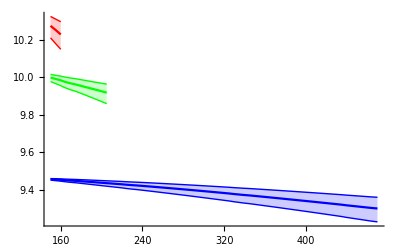

```mathematica
ListPlot[{Transpose[{Tscanb[[;;bb1Tmelt]],wrfitbb[[;;bb1Tmelt,1]]}],Transpose[{Tscanb[[;;bb1Tmelt]],wrfitbbl[[;;bb1Tmelt,1]]}],Transpose[{Tscanb[[;;bb1Tmelt]],wrfitbbu[[;;bb1Tmelt,1]]}],Transpose[{Tscanb[[;;bb2Tmelt]],wrfitbb[[;;bb2Tmelt,2]]}],Transpose[{Tscanb[[;;bb2Tmelt]],wrfitbbl[[;;bb2Tmelt,2]]}],Transpose[{Tscanb[[;;bb2Tmelt]],wrfitbbu[[;;bb2Tmelt,2]]}],Transpose[{Tscanb[[;;bb3Tmelt]],wrfitbb[[;;bb3Tmelt,3]]}],Transpose[{Tscanb[[;;bb3Tmelt]],wrfitbbl[[;;bb3Tmelt,3]]}],Transpose[{Tscanb[[;;bb3Tmelt]],wrfitbbu[[;;bb3Tmelt,3]]}]},PlotRange->All,Filling->{1->{2},1->{3},4->{5},4->{6},7->{8},7->{9}},FillingStyle->Opacity[0.2],PlotStyle->{Blue,{Blue,Thin},{Blue,Thin},Green,{Green,Thin},{Green,Thin},Red,{Red,Thin},{Red,Thin}},Joined->True]
```

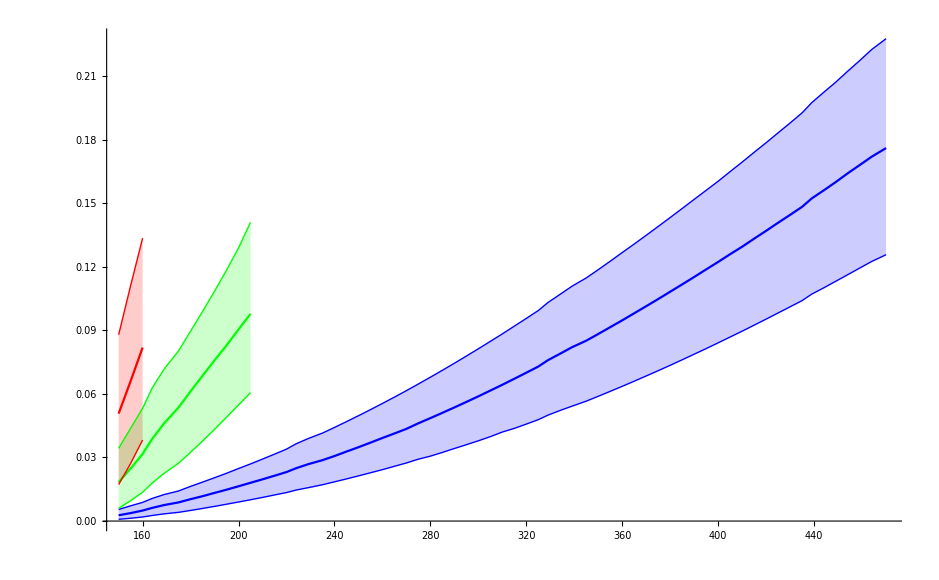

```mathematica
ListPlot[{Transpose[{Tscanb[[;;bb1Tmelt]],gfitbb[[;;bb1Tmelt,1]]}],Transpose[{Tscanb[[;;bb1Tmelt]],gfitbbl[[;;bb1Tmelt,1]]}],Transpose[{Tscanb[[;;bb1Tmelt]],gfitbbu[[;;bb1Tmelt,1]]}],Transpose[{Tscanb[[;;bb2Tmelt]],gfitbb[[;;bb2Tmelt,2]]}],Transpose[{Tscanb[[;;bb2Tmelt]],gfitbbl[[;;bb2Tmelt,2]]}],Transpose[{Tscanb[[;;bb2Tmelt]],gfitbbu[[;;bb2Tmelt,2]]}],Transpose[{Tscanb[[;;bb3Tmelt]],gfitbb[[;;bb3Tmelt,3]]}],Transpose[{Tscanb[[;;bb3Tmelt]],gfitbbl[[;;bb3Tmelt,3]]}],Transpose[{Tscanb[[;;bb3Tmelt]],gfitbbu[[;;bb3Tmelt,3]]}]},PlotRange->All,Filling->{1->{2},1->{3},4->{5},4->{6},7->{8},7->{9}},FillingStyle->Opacity[0.2],PlotStyle->{Blue,{Blue,Thin},{Blue,Thin},Green,{Green,Thin},{Green,Thin},Red,{Red,Thin},{Red,Thin}},Joined->True]
```

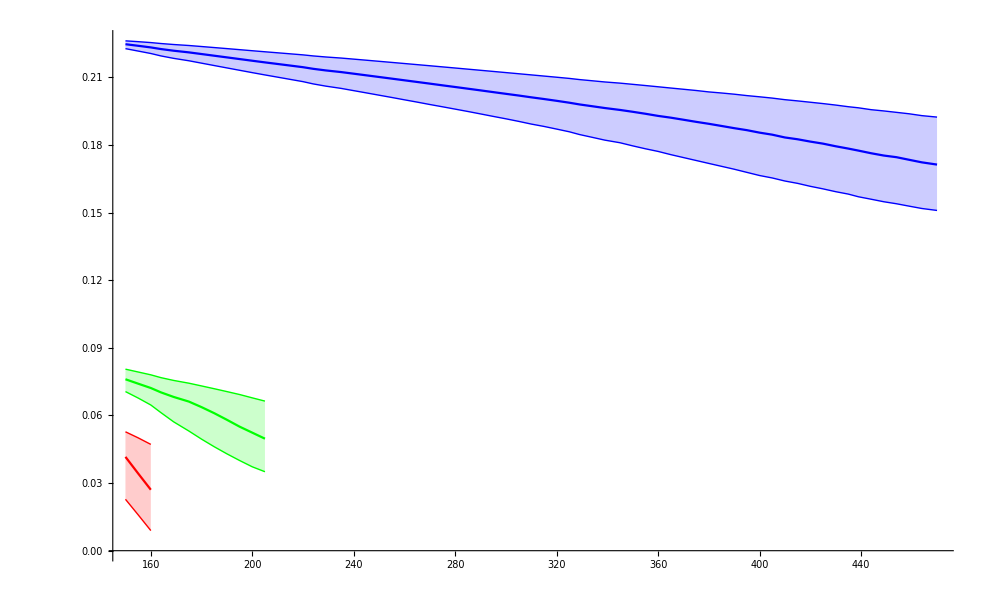

```mathematica
ListPlot[{Transpose[{Tscanb[[;;bb1Tmelt]],areafitbb[[;;bb1Tmelt,1]]}],Transpose[{Tscanb[[;;bb1Tmelt]],areafitbbl[[;;bb1Tmelt,1]]}],Transpose[{Tscanb[[;;bb1Tmelt]],areafitbbu[[;;bb1Tmelt,1]]}],Transpose[{Tscanb[[;;bb2Tmelt]],areafitbb[[;;bb2Tmelt,2]]}],Transpose[{Tscanb[[;;bb2Tmelt]],areafitbbl[[;;bb2Tmelt,2]]}],Transpose[{Tscanb[[;;bb2Tmelt]],areafitbbu[[;;bb2Tmelt,2]]}],Transpose[{Tscanb[[;;bb3Tmelt]],areafitbb[[;;bb3Tmelt,3]]}],Transpose[{Tscanb[[;;bb3Tmelt]],areafitbbl[[;;bb3Tmelt,3]]}],Transpose[{Tscanb[[;;bb3Tmelt]],areafitbbu[[;;bb3Tmelt,3]]}]},PlotRange->All,Filling->{1->{2},1->{3},4->{5},4->{6},7->{8},7->{9}},FillingStyle->Opacity[0.2],PlotStyle->{Blue,{Blue,Thin},{Blue,Thin},Green,{Green,Thin},{Green,Thin},Red,{Red,Thin},{Red,Thin}},Joined->True]
```